63.6364

{8.15524,13.4608,20.1038}

19.5069

0.0512639

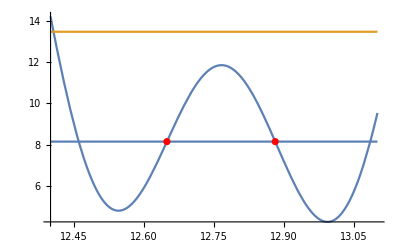

```mathematica
λ=1.064;
k=(2π)/λ;
θxy=10.8Degree;

Vxy=(2000.*0.14)/4.4
Vz=52.1/4.4;

V[z_]:=Vxy*(1-Sin[k Sin[θxy] z]^2)+Vz*(1-Sin[k z]^2)
z1=12.2;
z2=z/.FindRoot[V'[z]==0,{z,12.7}];

ees=Table[ee/.FindRoot[NIntegrate[Re[k √(ee-V[z])],{z,z1,z2}]==π(n+1/2),{ee,10}],{n,0,2}]//Quiet

z2=z/.FindRoot[(V[z]==ee /. ee-> ees[[1]]),{z,12.65}];
z3=z/.FindRoot[(V[z]==ee /. ee-> ees[[1]]),{z,12.85}];
ssq=Exp[-2 NIntegrate[Re[k √(V[z]-ee)]/.ee-> ees[[1]], {z, z2, z3}]];
tau=2 2 π 1/(ees[[1]]*4.4)1/ssq
t=1/tau

pltx0=12.4;
pltx1=13.1;
Show[
Plot[V[z],{z,pltx0,pltx1}],
Plot[Evaluate[ees],{z,pltx0,pltx1}],
ListPlot[{{z2,V[z2]},{z3,V[z3]}},PlotStyle->Red]
]
```

```mathematica
vTrap=100.;
vv=2 √(vTrap 4.4);
setPoint=x/.FindRoot[137.486(-0.00613+x)^0.638==vv,{x,0.2}]
```

0.161728

```mathematica
18.0*Sqrt[1/2]
```

12.7279

```mathematica
ωzz=137.486(-0.00613+0.1)^0.638
1/4 ωzz^2/4.4
```

30.39

52.4745

```mathematica
(5.kHz)^2/25ms
```

```mathematica
1. kHz
```

```mathematica
Γ=-1/(2π)Log[1/2]
```

```mathematica
Γ=-1/(2π)Log[1/2]=2π t^2/(60.kHz/(1ms))
```

Set::write: Tag Times in -(-Log[2])/(2 π) is Protected.

(1.98552×10^-8 ms)/kHz

```mathematica
-(1/(2π))^2 Log[1/2]((5.kHz)/(25.ms))=t^2
```

```mathematica
√(-(1/(2π))^2 Log[1/2]((60.kHz)/(1.ms)))/.{ms->1./kHz}
```

1.02638 √(kHz^2)

```mathematica
1G/cm/amps * 4volts * 16.6 amps/volts
```

(66.4 G)/cm

```mathematica
532nm * (66.4 G)/cm/.{nm->10^-9 m,cm->10^-2 m}
```

```mathematica
1400 kHz/G * 0.00353248 G
```

4.94547 kHz

```mathematica
ees
```

{8.15524,13.4608,20.1038}

```mathematica
ees[[1]]
```

8.15524

```mathematica
t
```

0.0512639